```mathematica
s01=0.5*x^101;
s02=0.5*x^101;
```

```mathematica
f[state_]:=state/2+state*x/2//Expand//Chop
g[state_]:=state/(2*x)+state/2//Expand//Chop
```

```mathematica
prbs=CoefficientList[Nest[f,s01,10]+Nest[g,s02,10],x,{202}][[2;;]];
```

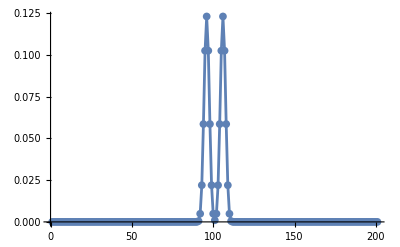

```mathematica
ListLinePlot[prbs,
PlotRange->All,
Mesh->All
]
```

```mathematica
hills=ArrayPad[#/2,{0,201-Length[#]}]+ArrayPad[#/2,{201-Length[#],0}]&@(N[Binomial[#,Range[0,#]]/2^#]&@10)//Chop;
```

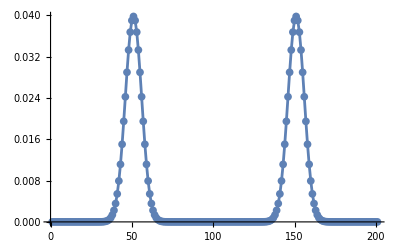

```mathematica
ListLinePlot[hills,
PlotRange->All,
Mesh->All
]
```

```mathematica
Abs[hills-prbs]//Chop//Max
```

1.20121×10^-10

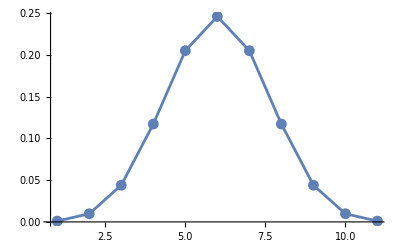

```mathematica
ListLinePlot[#,
PlotRange->All,
Mesh->All
]&@Chop[N[Binomial[#,Range[0,#]]/2^#]&@10]
```